{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→10,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

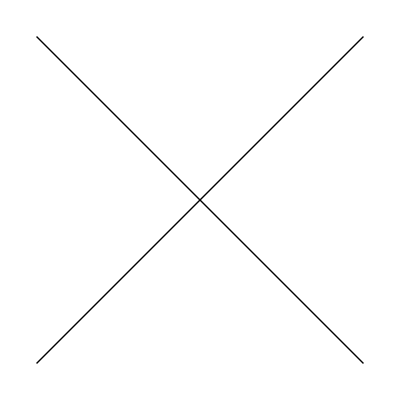
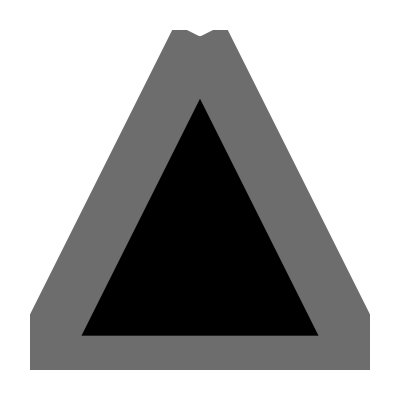
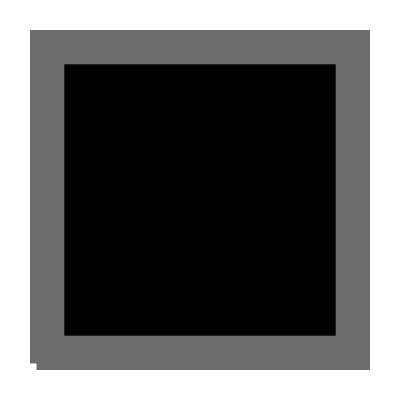
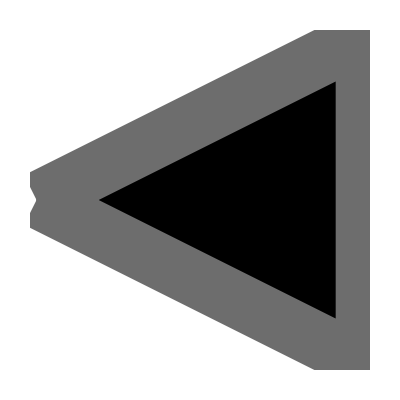
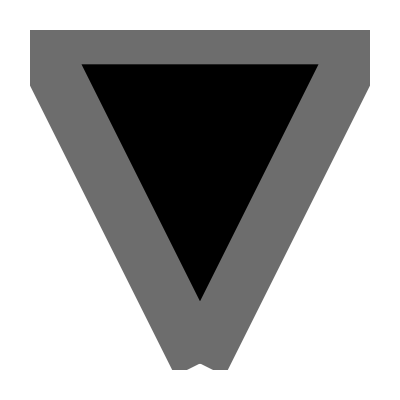
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
<<MaTeX`
myblue=RGBColor[0.2745098039,0.5333333333,0.9450980392];
myred=RGBColor[0.9176470588,0.2588235294,0.2078431373];
mygreen=RGBColor[0.2039215686,0.662745098,0.3176470588];
myyellow=RGBColor[0.9764705882,0.7333333333,0.1764705882];
mygray=RGBColor[109/255//N,109/255//N,109/255//N];
mylightgray=RGBColor[185/255//N,185/255//N,185/255//N];
thickness=0.015;
size=0.05;
font="Latin Modern Roman";
imagSize=200;
fontSize=10;
markersize=0.025;
cm=72/2.54;
ts=0.02*{1,1/GoldenRatio};

SetOptions[MaTeX,FontSize->fontSize]
SetOptions[MatrixPlot,FrameTicksStyle->Black,FrameStyle->Directive[FontFamily->font,FontSize->fontSize,FontColor->Black],ImageSize->imagSize,AspectRatio->1];
SetOptions[ListPlot,FrameStyle->Directive[FontFamily->font,FontSize->fontSize,FontColor->Black],Frame->True,Axes->False,ImageSize->imagSize,GridLines->Automatic,AspectRatio->1,FrameTicksStyle->Black,
PlotStyle->{{Thickness[thickness],myyellow},{Thickness[thickness],myblue},{Thickness[thickness],myred},{Thickness[thickness],mygreen}},Joined->True];
SetOptions[ListPlot,FrameStyle->Directive[FontFamily->font,FontSize->fontSize,FontColor->Black],Frame->True,Axes->False,ImageSize->imagSize,GridLines->Automatic,AspectRatio->1,FrameTicksStyle->Black,
PlotStyle->{{Thickness[thickness],myyellow},{Thickness[thickness],myblue},{Thickness[thickness],myred},{Thickness[thickness],mygreen}},Joined->True];
SetOptions[ListDensityPlot,FrameStyle->Directive[FontFamily->font,FontSize->fontSize,FontColor->Black],Frame->True,Axes->False,ImageSize->imagSize,GridLines->Automatic,AspectRatio->1,FrameTicksStyle->Black];
SetOptions[Plot,FrameStyle->Directive[FontFamily->font,FontSize->fontSize,FontColor->Black],Frame->True,Axes->False,ImageSize->imagSize,GridLines->Automatic,AspectRatio->1,FrameTicksStyle->Black,
PlotStyle->{{Thickness[thickness],myyellow},{Thickness[thickness],myblue},{Thickness[thickness],myred},{Thickness[thickness],mygreen}}];
SetOptions[DensityPlot,FrameStyle->Directive[FontFamily->font,FontSize->fontSize,FontColor->Black],Frame->True,Axes->False,ImageSize->imagSize,GridLines->Automatic,AspectRatio->1,FrameTicksStyle->Black];
align = Sequence[AlignmentPoint -> {0, 0}, AxesOrigin -> {0, 0}, BaselinePosition -> Axis];
size = Sequence[PlotRange -> {{-2, 2}, {-2, 2}}, PlotRangePadding -> Scaled[edgeThickness/2 + plotRangePadding], ImagePadding -> 0, ImageMargins -> 0];
plotRangePadding = .01;
edgeThickness = .1;
size = Sequence[PlotRange -> {{-2, 2}, {-2, 2}}, PlotRangePadding -> Scaled[edgeThickness/2 + plotRangePadding], ImagePadding -> 0, ImageMargins -> 0];
halfTr = {Graphics[{EdgeForm[{mygray, Thickness[edgeThickness], JoinForm["Round"]}], Line[{{-1, -1}, {1, 1}}], Line[{{-1, 1}, {1, -1}}](*EdgeForm[],FaceForm[Opacity[1]],Polygon[{{0,2},{2/Sqrt[3],0},{-(2/Sqrt[3]),0}}],EdgeForm[{Opacity[1],Thickness[edgeThickness],JoinForm["Round"]}],FaceForm[],Polygon[{{0,2},{Sqrt[3],-1},{-Sqrt[3],-1}}]*)}, align],
   Graphics[{EdgeForm[{mygray, Thickness[edgeThickness], JoinForm["Round"]}], Polygon[{{0, 1}, {1, -1}, {-1, -1}}]}, align],
   Graphics[{EdgeForm[{mygray, Thickness[edgeThickness], JoinForm["Round"]}], Rectangle[{-1, -1}, {1, 1}]}, align]};
halfTr = Flatten[{halfTr, Table[halfTr /. p : {_?NumericQ, _?NumericQ} :> RotationMatrix[θ].p, {θ, {Pi/2,  Pi}}]}, 2] /. "size" -> size
Magnify[#, .1] & /@ halfTr;
ListPlot[Flatten[Table[{{n, y}}, {y, Range[1, 3]}, {n, 20}], 1], PlotMarkers -> Table[{s, 0.07}, {s, halfTr}], PlotStyle -> ColorData[60, "ColorList"], GridLines -> {Range[20], Range[3]}, PlotRange -> {{0, 21}, {0, 4}}, Axes -> False, Frame -> True];

new={{"GoogleGradient","",{}},{"Gradients"},1,{0,1},{myblue,Lighter[myblue,.5],Lighter[myblue,.75],White,Lighter[myred,.75],Lighter[myred,.5],myred},""};
ColorData["GoogleGradient"]//Quiet;
AppendTo[DataPaclets`ColorDataDump`colorSchemes,new];
AppendTo[DataPaclets`ColorDataDump`colorSchemeNames,new[[1,1]]];
```

```mathematica
Clear[Uz,hx,hy,Uz,Hkin,f,U,J,Jpr,k,h,j,jpr]
f[k]=j+jpr*ⅇ^(ⅈ*k);
hx[k_]=j+jpr*Cos[k];
hy[k_]=-jpr*Sin[k];
h[k_]=√(hx[k]^2+hy[k]^2);
w[k_]=(hx[k]-ⅈ*hy[k])/h[k];
ϕ[k_]=If[hx[k]<0,π,0]+If[hx[k]>0&&hy[k]>0,2π,0]+ArcTan[-hy[k]/hx[k]];
U[k_]=1/(√2){{1, -w[k]},{w[k]*,1}};
Hkin[k_]=h[k]*{{0,w[k]},{w[k]*,0}};
```

```mathematica
Manipulate[Chop[Eigenvalues[Hkin[k]]],{k,0,2π}]
Manipulate[Chop[U[k]†.Hkin[k].U[k]]//MatrixForm,{k,0,2π}]
Manipulate[Chop[U[k]†.PauliMatrix[3].U[k]]//MatrixForm,{k,0,2π}]
Manipulate[{Chop[w[k]-ⅇ^(ⅈ*ϕ[k])],w[k],ⅇ^(ⅈ*ϕ[k])},{k,0,2π}]
Plot[ϕ[k],{k,0,2π}]
```

-Graphics-

```mathematica
(* diagonalize the SSH chain *)
diagonalizeSpinlessSSH[L_,pbc_,dt_,amp_,σx_]:=Module[{H,Ekin,Epot,eval,pot,t1,Ug,order, δt,t},
pot[x_,sigmax_,x0_]:=PDF[NormalDistribution[x0,sigmax],x];
t1[i_]:=If[EvenQ[i],1,dt];
H=ConstantArray[0,{L,L}];
Ekin=ConstantArray[0,{L,L}];
Epot=ConstantArray[0,{L,L}];
Do[
Ekin[[i,i+1]]+=t1[i];
Epot[[i,i]]+=Chop[amp/2*(i-L/2-.5)^2]
(*pot[i,σx,L/2];*)
,{i,1,L-1}];
Epot[[L,L]]+=amp/2*(L-L/2-.5)^2;
If[pbc==True,Ekin[[L,1]]+=t1[L]];
Ekin = Ekin + Ekin†;
Ekin = Ekin/.{δt->dt,t->1.0};
Epot = Epot/.{δt->dt,t->1.0};
H = Ekin + Epot;
{eval,Ug}=Eigensystem[H];
order = Ordering[eval];
eval=eval[[order]];
Ug=Ug[[order]];
Table[Ug[[i]]=Normalize[Ug[[i]]],{i,Length[Ug]}];
{eval,Ug, H, Ekin, Epot}];
```

```mathematica
j=.82;
jpr=1.;
analytics=ListPlot[Table[{tee,2NIntegrate[D[ϕ[k],k]*(1-Cos[2*h[k]*N[tee]])/4/π,{k,0,2π}]},{tee,0,40,0.1}],Joined->True,PlotStyle->Black];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

```mathematica
numerics={};
Do[
{eva,eve,ham,T,V}=diagonalizeSpinlessSSH[len,False,j,0,0];
start=ConstantArray[0,len];
start[[len/2-1]]=1;
next=start;
evo=MatrixExp[ⅈ*ham*0.01];
next=evo†.next;
list=Table[Abs[next=evo.next]^2/.{t->tee},{tee,0,4000,1}];
X=Table[i-Floor[(len+2)/4],{i,len/2}];
GammaX=Flatten[{X,-X}ᵀ];
AppendTo[numerics,Table[2GammaX.ls,{ls,list}]]
,{len,{64,128,256}}];
```

```mathematica
legend1 =LineLegend[{myyellow,myblue,myred,Black},{MaTeX["L=32"],MaTeX["L=64"],MaTeX["L=128"],MaTeX["\\text{Eq. (S.15)}"]},LegendLayout->"Column",LegendMarkerSize->15,Spacings->0.1]
```

```mathematica
op=1;
fs=0.2;
p1=ListPlot[numerics[[1]],DataRange->{0,40},PlotMarkers->None,Joined->True,PlotRange->Full,PlotRangePadding->0,PlotStyle->Thickness[.025],ColorFunction->Function[{x,y},If[x>0.36,{myyellow,Opacity[op(1-(x-.36)^fs)]},myyellow]],PlotLegends->Placed[legend1,{Left,Bottom}]];
p2=ListPlot[numerics[[2]],DataRange->{0,40},PlotMarkers->None,Joined->True,PlotRange->Full,PlotRangePadding->0,PlotStyle->Thickness[.02],ColorFunction->Function[{x,y},If[x>0.85,{myblue,Opacity[op(1-(x-.85)^fs)]},myblue]]];
p3=ListPlot[numerics[[3]],DataRange->{0,40},PlotMarkers->None,Joined->True,PlotRange->Full,PlotRangePadding->0,PlotStyle->Thickness[.015],ColorFunction->Function[{x,y},If[x>1,{myred,Opacity[op(1-(x-1)^fs)]},myred]]];
ticks={{Join[Table[{i,MaTeX[i],ts},{i,-1,1,1}],Table[{i,"",0.5*ts},{i,-.5,1.5,1}],{{2,"",ts}},{{1.78,MaTeX["\\Delta\\mathcal C"],ts*0}}],Join[]},{Join[Table[{i,MaTeX[i],ts},{i,0,35,10}],Table[{t,"",0.5*ts},{t,5,40,10}],{{38,MaTeX["tJ'"],.0}}],{None}}};
fs1=Show[p1,p2,p3,analytics,PlotRange->{{0,40},{-1,2}},FrameTicks->ticks,ImageSize->8.6cm,AspectRatio->1/GoldenRatio,GridLines->{{{15,Directive[myyellow,Dotted,Thickness[0.025]]},{35,Directive[myblue,Dotted,Thickness[0.025]]}},{0,1}},GridLinesStyle->Directive[{mygray,Thick,Dotted,Opacity[1]}],ImagePadding->(ip={{27,2},{18,2}})]
```

-Graphics-

```mathematica
numerics={};
Do[
{eva,eve,ham,T,V}=diagonalizeSpinlessSSH[len,False,j,0,0];
start=ConstantArray[0,len];
start[[len/2]]=1;
next=start;
evo=MatrixExp[-ⅈ*ham*0.05];
next=evo†.next;
list=Table[Abs[next=evo.next]^2/.{t->tee},{tee,0,800,1}];
X=Table[i-Floor[(len+2)/4],{i,len/2}];
GammaX=Flatten[{X,-X}ᵀ];
AppendTo[numerics,Table[2GammaX.ls,{ls,list}]]
,{len,{64,128,256}}];
```

```mathematica
ticks={{Join[Table[{i,MaTeX[i-65],ts},{i,5,120,20}],Table[{i,"",0.5*ts},{i,15,120,20}],{{122,MaTeX["x"],ts*0}}],Join[]},{Join[Table[{i,MaTeX[i],ts},{i,0,35,10}],Table[{t,"",0.5*ts},{t,5,40,10}],{{38,MaTeX["tJ'"],.0}}],{None}}};
fs2=Show[ListPlot[{},PlotRange->{{0,40},{1.,128}},AspectRatio->1/GoldenRatio,FrameTicks->ticks],ListDensityPlot[(list[[;;,;;;;2]]+list[[;;,2;;;;2]])ᵀ,DataRange->{{0,40},{2.,129.}},ColorFunction->"PigeonTones",PlotRange->{0,0.05},Frame->True,FrameStyle->Black,PlotRangePadding->0],ImageSize->8.6cm,GridLines->{{{15,Directive[{myyellow,Dotted,Thickness[0.025]}]},{35,Directive[{myblue,Dotted,Thickness[0.025]}]}},{{65-16,Directive[myyellow,Thickness[0.005]]},{65+15,Directive[myyellow,Thickness[0.005]]},{65-32,Directive[myblue,Thickness[0.005]]},{65+31,Directive[myblue,Thickness[0.005]]}}},GridLinesStyle->Opacity[1],Method->{"GridLinesInFront"->True},PlotRange->{{0,40},{2,129}},ImagePadding->ip]
```

-Graphics-

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/andreas/Desktop

```mathematica
Export["fs_single_particle_1.png",fs1,ImageResolution->600]
Export["fs_single_particle_2.png",fs2,ImageResolution->600]
```

fs_single_particle_1.png

fs_single_particle_2.png

```mathematica
L=256;  (* size of the system, can easily be up to ~1000 *)
enne=L/2;  (* Number of fermions *)
σx=4.; (* variance of the Gaussian potential *)
amp=0.0 10^-3;
(*amp=0.0;*)
pbc=False;
tmax= L;
Δt=tmax/100;
dt=j;
qpos=L/2;

Q=ConstantArray[0,L];
(*Q[[qpos-1]]=1;*)
Q[[qpos]]=1;

{e0,U0, H0, T0, V0}=Chop[diagonalizeSpinlessSSH[L,pbc,dt,amp,σx]]; (* diagonalizes the SSH Hamiltonian and returns the rotation, the Hamiltonian, kinetic and potential energy*)
(*enne=Length[Select[e0,#<0&]];*)

(* trafo lattice -> diag *)
Chop[U0.H0.U0†]//MatrixPlot;

(* trafo diag -> lattice *)
Chop[U0†.DiagonalMatrix[e0].U0]//MatrixPlot;

(* calculate the norm of the quenched state *)
P=U0.Q;
Clear[ΩM, ΩP];
ΩP[enne_]:=Norm[P[[enne+1;;]]]^2;
ΩM[enne_]:=Norm[P[[;;enne]]]^2;

(* create the chiral average position operator *)
X=Table[i-Floor[(L+2)/4],{i,L/2}];
GammaX=Flatten[{X,-X}ᵀ];

(* time evolution operator in diagonal basis *)
Clear[A];
A[t_,ev_]:=N[DiagonalMatrix[ⅇ^(-ⅈ*ev*t)]];
(* spectrum of the Hamiltonian *)
(* in case of trapped particles in a harmonic potential, the low-energy spectrum is linear according to Subscript[E, n]= ℏω(n + 1/2) *)
Show[ListPlot[e0-Min[e0],Joined->False],Plot[Sqrt[2amp](x+1/2),{x,0,L},PlotStyle->Black]];
(* single particle Green's for the ground state*)
G0=U0ᵀ[[;;,;;enne]].U0*[[;;enne,;;]];
(* ground state density distribution *)
ListPlot[Diagonal[G0],PlotRange->Full,FrameLabel->MaTeX[{"i","n_i"}]];
(* single particle greens of the quenched WP *)
Clear[GQP,GQM];
GQP[t_,enne_]:=N[U0†[[;;,;;enne]].U0[[;;enne,;;]]+Chop[If[t≥ 0, 1.0, 0.0]*1/ΩP[enne]{(U0†[[;;,enne+1;;]].A[t,e0]*[[enne+1;;,enne+1;;]].P[[enne+1;;]])}ᵀ.{(P*[[enne+1;;]].A[t,e0][[enne+1;;,enne+1;;]].U0[[enne+1;;,;;]])}]];
GQM[t_,enne_]:=Chop[U0†[[;;,;;enne]].U0[[;;enne,;;]]+If[t≥ 0, 1.0, 0.0]*-1/ΩM[enne]{Chop[N[(U0†[[;;,;;enne]].A[t,e0]*[[;;enne,;;enne]].P[[;;enne]])]]}ᵀ.{Chop[N[(P*[[;;enne]].A[t,e0][[;;enne,;;enne]].U0[[;;enne,;;]])]]}];
devo=Table[Chop[Diagonal[GQP[t,enne]]],{t,-0.05,40,.05}];
ticks={{Join[Table[{i,MaTeX[i-65],ts},{i,5,120,20}],Table[{i,"",0.5*ts},{i,15,120,20}],{{122,MaTeX["x"],ts*0}}],Join[]},{Join[Table[{i,MaTeX[i],ts},{i,0,35,10}],Table[{t,"",0.5*ts},{t,5,40,10}],{{38,MaTeX["tJ'"],.0}}],{None}}};
fs4=Show[ListPlot[{},PlotRange->{{0,40},{1.,128}},AspectRatio->1/GoldenRatio,FrameTicks->ticks],ListDensityPlot[(devo[[;;,;;;;2]]+devo[[;;,2;;;;2]])ᵀ,DataRange->{{0,40},{2.,129.}},ColorFunction->"PigeonTones",PlotRange->{.9999,1.05},Frame->True,FrameStyle->Black,PlotRangePadding->0],ImageSize->8.6cm,GridLines->{{{15,Directive[{myyellow,Dotted,Thickness[0.025]}]},{35,Directive[{myblue,Dotted,Thickness[0.025]}]}},{{65-16,Directive[myyellow,Thickness[0.005]]},{65+15,Directive[myyellow,Thickness[0.005]]},{65-32,Directive[myblue,Thickness[0.005]]},{65+31,Directive[myblue,Thickness[0.005]]}}},GridLinesStyle->Opacity[1],Method->{"GridLinesInFront"->True},PlotRange->{{0,40},{2,128.5}},ImagePadding->ip];
```

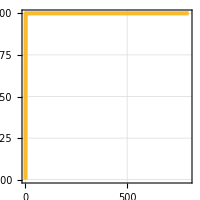

```mathematica
(*numericsFS={};*)
mcd=Table[2*GammaX.(ls-devo[[1]]),{ls,devo}];
(*mcd=Table[2*GammaX.(ls),{ls,devo}];*)
ListPlot[mcd]
AppendTo[numericsFS,mcd];
```

```mathematica
legend2 =LineLegend[{myyellow,myblue,myred,Black},{MaTeX["L=32"],MaTeX["L=64"],MaTeX["L=128"],MaTeX["\\text{Eq. (S.16)}"]},LegendLayout->"Column",LegendMarkerSize->15,Spacings->0.1]
```

```mathematica
op=1;
fs=0.2;
p1=ListPlot[numericsFS[[1,2;;]],DataRange->{0,40},PlotMarkers->None,Joined->True,PlotRange->Full,PlotRangePadding->0,PlotStyle->Thickness[.025],ColorFunction->Function[{x,y},If[x>0.36,{myyellow,Opacity[op(1-(x-.36)^fs)]},myyellow]],PlotLegends->Placed[legend2,{Left,Bottom}]];
p2=ListPlot[numericsFS[[2,2;;]],DataRange->{0,40},PlotMarkers->None,Joined->True,PlotRange->Full,PlotRangePadding->0,PlotStyle->Thickness[.02],ColorFunction->Function[{x,y},If[x>0.85,{myblue,Opacity[op(1-(x-.85)^fs)]},myblue]]];
p3=ListPlot[numericsFS[[3,2;;]],DataRange->{0,40},PlotMarkers->None,Joined->True,PlotRange->Full,PlotRangePadding->0,PlotStyle->Thickness[.015],ColorFunction->Function[{x,y},If[x>1,{myred,Opacity[op(1-(x-1)^fs)]},myred]]];
ticks={{Join[Table[{i,MaTeX[i],ts},{i,-.8,.95,0.05}],Table[{i,"",0.5*ts},{i,.825,.975,.05}],{{1,"",ts}},{{1,MaTeX["\\Delta\\mathcal C"],ts*0}}],Join[]},{Join[Table[{i,MaTeX[i],ts},{i,0,35,10}],Table[{t,"",0.5*ts},{t,5,40,10}],{{38,MaTeX["tJ'"],.0}}],{None}}};
analytics = ListPlot[{{0,1},{45,1}},PlotStyle->{Black,Thick}];
fs3=Show[p1,p2,p3,analytics,PlotRange->{{0,40},{0.8,1.01}},FrameTicks->ticks,ImageSize->8.6cm,AspectRatio->1/GoldenRatio,GridLines->{{{15,Directive[myyellow,Dotted,Thickness[0.025]]},{35,Directive[myblue,Dotted,Thickness[0.025]]}},{0,1}},GridLinesStyle->Directive[{mygray,Thick,Dotted,Opacity[1]}],ImagePadding->(ip={{27,2},{18,2}})]
```

-Graphics-

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/andreas/Desktop

```mathematica
Export["fs_groundstate_1.png",fs3,ImageResolution->600]
Export["fs_groundstate_2.png",fs4,ImageResolution->600]
```

fs_groundstate_1.png

fs_groundstate_2.png